```mathematica
40000*12
```

480000

```mathematica
64*4
```

256

```mathematica
15 * 40
```

600

```mathematica
ylafu[x1,ep,ep]+ylafu[x1,ep,ep]
```

2 ylafu[x1,ep,ep]

```mathematica
ylafu[x1,ep,ep]+ylafu[x2,ep,ep]  == ylafu[x2,ep,ep]+ylafu[x1,ep,ep]
```

True

```mathematica
X = fun[em,em,em]-fun[x1,em,em]-fun[em,y1,em]-fun[em,em,z1]-fun[x1,y1,z1]+fun[x1,y1,em]+fun[x1,em,z1]+fun[em,y1,z1]+fun[x2,em,em]-fun[ep,em,em]-fun[x2,y1,em]-fun[x2,em,z1]-fun[ep,y1,z1]+fun[ep,y1,em]+fun[ep,em,z1]+fun[x2,y1,z1]+fun[ep,y2,ep]-fun[x1,y2,ep]-fun[ep,ep,ep]-fun[ep,y2,z1]-fun[x1,ep,z1]+fun[x1,ep,ep]+fun[x1,y2,z1]+fun[ep,ep,z1]+fun[ep,ep,z2]-fun[x1,ep,z2]-fun[ep,y1,z2]-fun[ep,ep,ep]-fun[x1,y1,ep]+fun[x1,y1,z2]+fun[x1,ep,ep]+fun[ep,y1,ep]+fun[x2,y2,ep]-fun[ep,y2,ep]-fun[x2,ep,ep]-fun[x2,y2,z1]-fun[ep,ep,z1]+fun[ep,ep,ep]+fun[ep,y2,z1]+fun[x2,ep,z1]+fun[x2,ep,z2]-fun[ep,ep,z2]-fun[x2,y1,z2]-fun[x2,ep,ep]-fun[ep,y1,ep]+fun[ep,y1,z2]+fun[ep,ep,ep]+fun[x2,y1,ep]+fun[ep,y2,z2]-fun[x1,y2,z2]-fun[ep,ep,z2]-fun[ep,y2,ep]-fun[x1,ep,ep]+fun[x1,ep,z2]+fun[x1,y2,ep]+fun[ep,ep,ep]+fun[x2,y2,z2]-fun[ep,y2,z2]-fun[x2,ep,z2]-fun[x2,y2,ep]-fun[ep,ep,ep]+fun[ep,ep,z2]+fun[ep,y2,ep]+fun[x2,ep,ep];
```

```mathematica
Y = fun[ep,ep,ep]-fun[x1,ep,ep]-fun[ep,y1,ep]-fun[ep,ep,z1]-fun[x1,y1,z1]+fun[x1,y1,ep]+fun[x1,ep,z1]+fun[ep,y1,z1]+fun[x2,ep,ep]-fun[ep,ep,ep]-fun[x2,y1,ep]-fun[x2,ep,z1]-fun[ep,y1,z1]+fun[ep,y1,ep]+fun[ep,ep,z1]+fun[x2,y1,z1]+fun[ep,y2,ep]-fun[x1,y2,ep]-fun[ep,ep,ep]-fun[ep,y2,z1]-fun[x1,ep,z1]+fun[x1,ep,ep]+fun[x1,y2,z1]+fun[ep,ep,z1]+fun[ep,ep,z2]-fun[x1,ep,z2]-fun[ep,y1,z2]-fun[ep,ep,ep]-fun[x1,y1,ep]+fun[x1,y1,z2]+fun[x1,ep,ep]+fun[ep,y1,ep]+fun[x2,y2,ep]-fun[ep,y2,ep]-fun[x2,ep,ep]-fun[x2,y2,z1]-fun[ep,ep,z1]+fun[ep,ep,ep]+fun[ep,y2,z1]+fun[x2,ep,z1]+fun[x2,ep,z2]-fun[ep,ep,z2]-fun[x2,y1,z2]-fun[x2,ep,ep]-fun[ep,y1,ep]+fun[ep,y1,z2]+fun[ep,ep,ep]+fun[x2,y1,ep]+fun[ep,y2,z2]-fun[x1,y2,z2]-fun[ep,ep,z2]-fun[ep,y2,ep]-fun[x1,ep,ep]+fun[x1,ep,z2]+fun[x1,y2,ep]+fun[ep,ep,ep]+fun[x2,y2,z2]-fun[ep,y2,z2]-fun[x2,ep,z2]-fun[x2,y2,ep]-fun[ep,ep,ep]+fun[ep,ep,z2]+fun[ep,y2,ep]+fun[x2,ep,ep];
```

```mathematica
X-Y
```

fun[em,em,em]-fun[em,em,z1]-fun[em,y1,em]+fun[em,y1,z1]-fun[ep,em,em]+fun[ep,em,z1]+fun[ep,y1,em]-fun[ep,y1,z1]-fun[x1,em,em]+fun[x1,em,z1]+fun[x1,ep,ep]-fun[x1,ep,z1]+fun[x1,y1,em]-fun[x1,y1,ep]+fun[x2,em,em]-fun[x2,em,z1]-fun[x2,ep,ep]+fun[x2,ep,z1]-fun[x2,y1,em]+fun[x2,y1,ep]

## Different forms for the indefinite integral

```mathematica
FullSimplify[Integrate[1/((x^2+y^2+z^2)^(1/2)), x, y, z]]
```

1/4 (-2 (2 z^2 (-ArcTan[x/z]+ArcTan[(x y)/(z √(x^2+y^2+z^2))])+2 y^2 ArcTan[(x z)/(y √(x^2+y^2+z^2))]+x (2 z+x ArcTan[(y z)/(x √(x^2+y^2+z^2))]))+4 x y ArcTanh[z/(√(x^2+y^2+z^2))]+4 y z Log[x+√(x^2+y^2+z^2)]+z (4 x Log[y+√(x^2+y^2+z^2)]-ⅈ z (Log[(z+(ⅈ y (y+√(x^2+y^2+z^2)))/(x+ⅈ z))/(y^2 z^2)]-Log[(z+(y (y+√(x^2+y^2+z^2)))/(ⅈ x+z))/(y^2 z^2)]))+ⅈ y^2 (Log[(8 x y-8 ⅈ (y^2+z (z+√(x^2+y^2+z^2))))/((x-ⅈ y) y^2 z^2)]-Log[(8 x y+8 ⅈ (y^2+z (z+√(x^2+y^2+z^2))))/((x+ⅈ y) y^2 z^2)]))

```mathematica
D[1/(√(x^2+y^2+z^2)), x]
```

-x/((x^2+y^2+z^2)^(3/2))

```mathematica
f1 = Integrate[-x/((x^2+y^2+z^2)^(3/2)), x, y, z];
f1s = FullSimplify[f1/.{x^2+y^2+z^2->r^2}, r≥0]
```

-x ArcTan[(y z)/(r x)]+z ArcTanh[r/y]+y ArcTanh[r/z]

```mathematica
f2 = Integrate[-x/((x^2+y^2+z^2)^(3/2)), y,x, z];
f2s= FullSimplify[f2/.{x^2+y^2+z^2->r^2}, r≥0]
```

-x ArcTan[(y z)/(r x)]+y ArcTanh[r/z]+z Log[r+y]

```mathematica
f3 = Integrate[-x/((x^2+y^2+z^2)^(3/2)),x, z, y];
f3s= FullSimplify[f3/.{x^2+y^2+z^2->r^2}, r≥0]
```

-x ArcTan[(y z)/(r x)]+z ArcTanh[r/y]+y ArcTanh[r/z]

```mathematica
f4 = Integrate[-x/((x^2+y^2+z^2)^(3/2)),y, z, x];
f4s = FullSimplify[f4/.{x^2+y^2+z^2->r^2}, r≥0]
```

-x ArcTan[(y z)/(r x)]+z Log[r+y]+1/2 y (-Log[r-z]+Log[r+z])

```mathematica
f5 = Integrate[-x/((x^2+y^2+z^2)^(3/2)),z, x,y];
f5s = FullSimplify[f5/.{x^2+y^2+z^2->r^2}, r≥0]
```

-x ArcTan[(y z)/(r x)]+z ArcTanh[r/y]+y Log[r+z]

```mathematica
f6 = Integrate[-x/((x^2+y^2+z^2)^(3/2)),z, y,x];
f6s = FullSimplify[f6/.{x^2+y^2+z^2->r^2}, r≥0]
```

1/2 (-2 x ArcTan[(y z)/(r x)]-z Log[r-y]+z Log[r+y]+2 y Log[r+z])

```mathematica
(*Here is a form not found*)
FullSimplify[D[x*ArcTan[z/x]+x*ArcTan[(y*z)/(x*√(x^2+y^2+z^2))]-z*Log[(y+√(x^2+y^2+z^2))]-y*Log[(z+√(x^2+y^2+z^2))], x,y,z]]
```

x/((x^2+y^2+z^2)^(3/2))

```mathematica
0
```

```mathematica
flist0 = {f1, f2, f3, f4, f5, f6};
flist = {f1s, f2s, f3s, f4s, f5s, f6s};
```

```mathematica
#/.x->0 &/@flist
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

{Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate,Indeterminate}

```mathematica
Limit[#, z->0] &/@flist0
```

{Indeterminate,Indeterminate,Indeterminate,0,1/2 y Log[x^2+y^2],1/2 y Log[x^2+y^2]}

```mathematica
Limit[#, z->0] &/@flist
```

{Indeterminate,Indeterminate,Indeterminate,0,y Log[r],y Log[r]}

```mathematica
Plot3D[y Log[r]/. r->√(x^2+y^2), {x, -1,1}, {y,-1,1}]
```

-Graphics3D-

## Evaluate indefinite integral

```mathematica
a = 1;
Integrate[-x/((x^2+y^2+z^2)^(3/2)), {x,-a,a}, {y,-a,a}, { z,-a,a}]
```

0

```mathematica
EvalInt[x1_, x2_, y1_,y2_,z1_,z2_,func_]:= func[x2,y2,z2]-func[x1,y2,z2]-func[x2,y1,z2]-func[x2,y2,z1]-func[x1,y1,z1]+func[x1,y1,z2]+func[x1,y2,z1]+func[x2,y1,z1]
```

```mathematica
EvalInt[-a,a,-a,a,-a,a,f1]
```

-(-x ArcTan[(y z)/(x √(x^2+y^2+z^2))]+z ArcTanh[(√(x^2+y^2+z^2))/y]+y ArcTanh[(√(x^2+y^2+z^2))/z])[-1,-1,-1]+(-x ArcTan[(y z)/(x √(x^2+y^2+z^2))]+z ArcTanh[(√(x^2+y^2+z^2))/y]+y ArcTanh[(√(x^2+y^2+z^2))/z])[-1,-1,1]+(-x ArcTan[(y z)/(x √(x^2+y^2+z^2))]+z ArcTanh[(√(x^2+y^2+z^2))/y]+y ArcTanh[(√(x^2+y^2+z^2))/z])[-1,1,-1]-(-x ArcTan[(y z)/(x √(x^2+y^2+z^2))]+z ArcTanh[(√(x^2+y^2+z^2))/y]+y ArcTanh[(√(x^2+y^2+z^2))/z])[-1,1,1]+(-x ArcTan[(y z)/(x √(x^2+y^2+z^2))]+z ArcTanh[(√(x^2+y^2+z^2))/y]+y ArcTanh[(√(x^2+y^2+z^2))/z])[1,-1,-1]-(-x ArcTan[(y z)/(x √(x^2+y^2+z^2))]+z ArcTanh[(√(x^2+y^2+z^2))/y]+y ArcTanh[(√(x^2+y^2+z^2))/z])[1,-1,1]-(-x ArcTan[(y z)/(x √(x^2+y^2+z^2))]+z ArcTanh[(√(x^2+y^2+z^2))/y]+y ArcTanh[(√(x^2+y^2+z^2))/z])[1,1,-1]+(-x ArcTan[(y z)/(x √(x^2+y^2+z^2))]+z ArcTanh[(√(x^2+y^2+z^2))/y]+y ArcTanh[(√(x^2+y^2+z^2))/z])[1,1,1]

```mathematica
-x ArcTan[(y z)/(r x)]+z ArcTanh[r/y]+y Log[r+z]/.z->0
```

y Log[r]

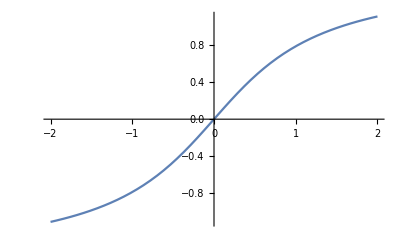

```mathematica
Plot[ArcTan[x], {x,-2,2}]
```

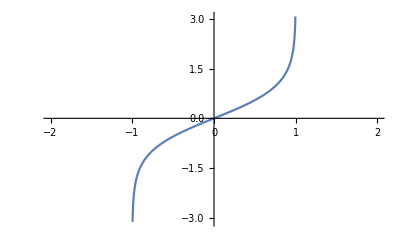

```mathematica
Plot[ArcTanh[x], {x,-2,2}]
```

```mathematica
Integrate[-x/((x^2+y^2+z^2)^(3/2)), {x, x0, x1}, {y, y0,y1}, {z, z0,z1}]
```

$Aborted

```mathematica
dr =.;
Integrate[-x/((x^2+y^2+z^2)^(3/2)), {x,0, dr}, {y,0, dr}, {z,0, dr}]
```

-1/6 √(dr^2) (π+12 (ArcTanh[√2]-ArcTanh[√3]))

```mathematica
Integrate[-x/((x^2+y^2+z^2)^(3/2)), {x,-dr, dr}, {y,-dr, dr}, {z,-dr, dr}]
```

ConditionalExpression[0,dr∈ℝ]

```mathematica
Integrate[1/((x^2+y^2+z^2)^(1/2)), {x,0, dr}, {y,0, dr}, {z,0, dr}]
```

∫_0^dr (-x ArcCot[(x √(2 dr^2+x^2))/dr^2]-1/2 dr (Log[dr^2+x^2]+Log[-dr+√(2 dr^2+x^2)]-3 Log[dr+√(2 dr^2+x^2)]))ⅆx

```mathematica
Integrate[1/((x^2+y^2+z^2)^(1/2)), {x,-dr, dr}, {y,-dr, dr}, {z,-dr, dr}]
```

2/3 dr (-12 ⅈ dr π+√(dr^2) π-3 dr Log[4]-6 dr Log[dr^2]-12 dr Log[-dr+√3 √(dr^2)]+24 dr Log[dr+√3 √(dr^2)]-3 ⅈ dr Log[-((1/2-ⅈ/2) ((2+ⅈ) dr+√3 √(dr^2)))/dr^3]-9 ⅈ dr Log[((1/2-ⅈ/2) ((2+ⅈ) dr+√3 √(dr^2)))/dr^3]+3 ⅈ dr Log[-((3+ⅈ) dr+(1+ⅈ) √3 √(dr^2))/(2 dr^3)]+9 ⅈ dr Log[((3+ⅈ) dr+(1+ⅈ) √3 √(dr^2))/(2 dr^3)])

```mathematica
FullSimplify[%22, dr >0]
```

2 dr^2 ((1-4 ⅈ) π+Log[1351+780 √3])